```mathematica
F[x1_,x2_,β1_,β2_]:=1/(1+Exp[-(β1 x1+β2 x2)])
```

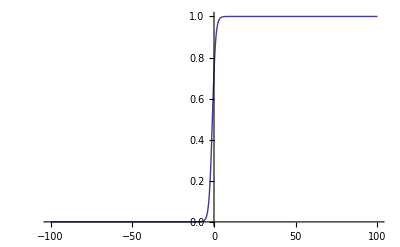

```mathematica
Plot[F[x,1,1,1],{x,-100,100}]
```

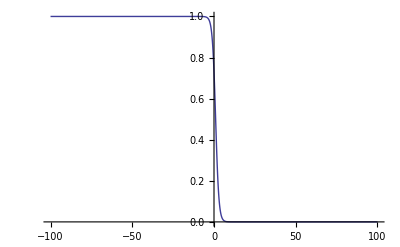

```mathematica
Plot[F[x,1,-1,1],{x,-100,100}]
```

```mathematica
Solve[{k x1+b==x2, x2/x1==-1/k },{x1,x2}]
```

{{x1→-(b k)/(1+k^2),x2→b/(1+k^2)}}

```mathematica
Simplify[((b k)/(1+k^2))^2+(b/(1+k^2))^2]
```

b^2/(1+k^2)